Mathematica >

# NRMMA - Numerical Relativity in Mathematica

NRMMA is a suite of Mathematica packages for analysing data in Numerical Relativity.  It has been designed for use with common output formats used by the Cactus code, with a focus on output from the PSU and AEI codes.

A large selection of NR-related functions are provided.  Includes interfaces to: read data from simulation output directories including waveforms, BH trajectories, apparent horizons, isolated horizons.  Extrapolation of radiated quantities to r = ∞.  Convergence testing.  Computation of strain from Psi4.  Reading grid structure values.  Exporting simulation data to a standard uniform format.

Load the package

```mathematica
<<nrmma`
```

## Getting Started

### Finding simulation directories

NRMMA has an interface for accessing "simulations" which are directories containing simulation output.  The name of the simulation is the name of the directory.  You can either specify a simulation by a full path, or by the simulation name.  For the latter, NRMMA needs to know which directory to look in.  You can set the variable RunDirectory to this directory and NRMMA will then know where to find your simulations. For example, in your init.m file you can set if you have your simulations in that directory.

Set the RunDirectory variable to the directory containing your simulations

```mathematica
RunDirectory=$HomeDirectory<>"/Simulations";
```

### Chunking

Simulations usually take more than one job on a supercomputer, and the output is spread across many different output directories ("chunks").  NRMMA supports the SimFactory chunking mechanism and almost all the file reading functions go through a layer which automatically merges the files in these chunks together, taking care to eliminate any duplicate data.  As such, you should never have to worry about merging chunks of data together, and in fact you can probably forget about the fact that the simulation data is split into chunks.

### DataTables and DataRegions

NRMMA uses the DataTable and DataRegion packages extensively to represent numerical simulation data, so you should also look at the documentation for those package to familiarise yourself with the concepts.

### Memoisation

Some functions use "memoisation".  In other words, the first time a particular quantity is accessed, for example a waveform, it is cached in memory so that later calls to the function do not have to read the data off the disk again.  When using very long simulations this can save a significant amount of time.  However, beware that if the run data on the disk changes, the copy in memory will not be.  To clear the cache, use the function ClearAllMemos. It would be possible to modify the caching algorithm to read the data again when it changes on disk, but this has not been done yet.

Clear data cache

```mathematica
ClearAllMemos[]
```

There are many functions in the NRMMA package contains functions for dealing with NR waveforms, BH trajectories, apparent horizons, run statistics, convergence testing and more.

In this tutorial we look at a binary black hole simulation

```mathematica
<<nrmma`
```

```mathematica
run = "q1D8";
```

## Waveforms

ReadPsi4 | Re
Phase | Im
Frequency | Abs

Functions for working with Numerical Relativity waveforms.

Read (2,2) mode of waveform extracted at r=100M from a simulation

```mathematica
psi4=ReadPsi4[run,2,2,100]
```

DataTable[...]

```mathematica
ListLinePlot[{Re[psi4],Im[psi4],Abs[psi4]},PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Phase[psi4],PlotRange->All]
```

-Graphics-

```mathematica
ListLinePlot[Frequency[psi4],PlotRange->{-1,1}]
```

-Graphics-

## Trajectories

These functions can be used with output from either PunctureTracker or MinTracker, and the latter could be used to track neutron stars.

ReadBHTrajectory | ReadBHSeparation
ReadBHCoordinates | ReadBHPhase

Functions for dealing with coordinate trajectories.

Puncture 0 trajectory

```mathematica
traj0=ReadBHTrajectory[run,0];
```

```mathematica
Take[traj0,10]
```

{{4,0},{3.99988,0.00581125},{3.99917,0.0367813},{3.99782,0.0842237},{3.99591,0.138268},{3.99353,0.193381},{3.99088,0.24797},{3.9879,0.302629},{3.98445,0.357576},{3.98052,0.412673}}

Puncture 1 trajectory

```mathematica
traj1=ReadBHTrajectory[run,1];
```

```mathematica
ListLinePlot[{traj0,traj1},PlotRange->All,AspectRatio->1]
```

-Graphics-

Separation of the BHs (radius of relative orbit)

```mathematica
ListLinePlot[ReadBHSeparation[run]]
```

-Graphics-

Phase of orbit

```mathematica
ListLinePlot[ReadBHPhase[run]]
```

-Graphics-

Individual coordinates

```mathematica
bh0x=ReadBHCoordinate[run,0,1];
```

```mathematica
ListLinePlot[bh0x]
```

-Graphics-

## Apparent Horizons

Remember that AHFinderDirect numbers its horizons from 1, not 0

Apparent horizon radius

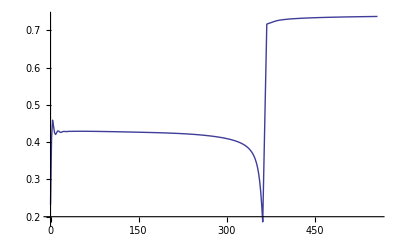

```mathematica
ListLinePlot[ReadAHRadius[run,1]]
```

Apparent horizon mass

```mathematica
ListLinePlot[ReadAHMass[run,1],PlotRange->{0,1}]
```

-Graphics-

## Isolated Horizons

IsolatedHorizon numbers horizons from 0

Spin of the first black hole

```mathematica
spin=ReadIsolatedHorizonSpin[run,0];
Take[ToList[spin],10]
```

{{0,{-2.72635×10^-16,4.20628×10^-18,-9.19887×10^-8}},{1.728,{-3.54358×10^-16,1.00605×10^-16,7.31241×10^-6}},{3.456,{-7.74157×10^-13,4.0053×10^-15,-1.12205×10^-6}},{5.184,{9.45366×10^-13,-1.35416×10^-13,-0.0000106483}},{6.912,{-5.84354×10^-13,3.26446×10^-14,-6.22614×10^-6}},{8.64,{1.82348×10^-12,-5.21059×10^-13,1.1512×10^-6}},{10.368,{-2.43463×10^-12,-1.50159×10^-13,8.33817×10^-6}},{12.096,{4.79914×10^-12,-1.94294×10^-11,0.0000887115}},{13.824,{6.52972×10^-13,3.8358×10^-12,0.0000868558}},{15.552,{2.50493×10^-12,1.39519×10^-11,0.0000119993}}}

```mathematica
ListLinePlot[Norm[spin],PlotRange->{-0.1,0.8}]
```

-Graphics-

RELATED TUTORIALS

CarpetHDF5

DataRegion

DataTable

Kicks